```mathematica
eqn2 = y''[x]+y[x]==Sin[x];
```

```mathematica
sol2 = DSolve[eqn2, y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]+1/4 (-2 x Cos[x]-2 Cos[x]^2 Sin[x]+Cos[x] Sin[2 x])}}

```mathematica
sol2plot1 = y[x]/.sol2/.{C[1]->1,C[2]->3};
```

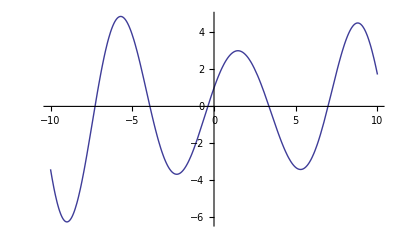

```mathematica
Plot[sol2plot1,{x,-10,10}]
```

```mathematica
eqn3 = y''[x]-2y'[x]+y[x]==Exp[x]Sin[x];
```

```mathematica
sol3 = DSolve[eqn3,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x x C[2]-ⅇ^x Sin[x]}}

```mathematica
eqn4a = x'[t]+y[t]==0;
```

```mathematica
eqn4b = y'[t]+x[t]==0;
```

```mathematica
sol4 = DSolve[{eqn4a,eqn4b},{x[t],y[t]},t]
```

{{x[t]→1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2],y[t]→-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]}}

```mathematica
eqn5 = y*D[u[x,y],x]+x*D[u[x,y],y]==0;
```

```mathematica
sol5 = DSolve[eqn5,u[x,y],{x,y}]
```

{{u[x,y]→C[1][1/2 (-x^2+y^2)]}}

```mathematica
Plot3D[u[x,y]/.sol5,{x,-10,10},{y,-10,10}]
```

-Graphics3D-